# grid and integration

## 1. Global constants and basic functions

```mathematica
hbar=1.0545718176461565*10^-27;
e=4.803204712570263*10^(-10);
me=9.1093837015*10^(-28);
mp=1.67262192369*10^-24;
A=1;Z=1;Ye=1;
kb=1.380649*10^(-16);
kev2erg=1.6021766339999998*10^-9;
c=29979245800.0;
σT=8*π/3*e^4/(c^4 me^2);
κT=σT/mp;
G=6.674299999999999*10^-8;
Ms=1.988409870698051*10^33;
km=10^5;
αF=e^2/(hbar c);
BQ=me^2*c^3/e/hbar;
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
C0[a_]:=1/a-Exp[a]*ExpIntegralE[1,a];
C1[a_]:=(1+a)*Exp[a]*ExpIntegralE[1,a]-1;
radian[x_]:=x/180*π;
Planck[Es_,T_]:=2*hbar*2*π*(Es*kev2erg/hbar/2/π)^3/c^2*1/(Exp[(Es*kev2erg)/(kb*T)]-1);
```

## Temperature profile

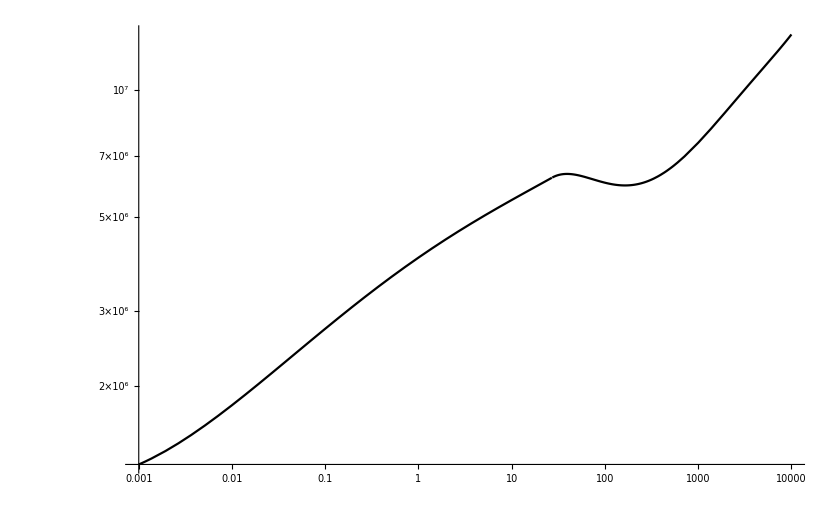

```mathematica
temperature[τ_]:=Module[{τmid,x},
τmid=27.1;
a1=0.793;
a2= 0.122;
a3=-0.502;
a4=0.548;
a5= -0.205;
a6=0.0266;
b3=0.00445;
b4=0.0108;
b5=0.00211;
b6=0.0000574;
x=Log[10,τ]-Log[10,τmid];
Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}]];
LogLogPlot[temperature[τ],{τ,0.001,10^4},Background->White,PlotTheme->"Monochrome"]
```

## Scatter opacity

```mathematica
Aint[Es_,B_,τ_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,ri,ϵp,ηp,g,ϵ,η,βi,K1i,K2i,Kz1i,Kz2i,ep1i,em1i,ep2i,em2i,e01i,e02i,Ap1,Am1,A01,Ap2,Am2,A02,Ap,Am,A0,ρ,x,T,Mns,Rns,gns,τmid,δv},
τmid=27.1;
a1=0.793;
a2= 0.122;
a3=-0.502;
a4=0.548;
a5= -0.205;
a6=0.0266;
b3=0.00445;
b4=0.0108;
b5=0.00211;
b6=0.0000574;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;

b=B/BQ;
δv=αF/(45 π)b^2;
(*turn on the vacuum*)
a=1-2*δv;
q=7δv;
m=-4δv;
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
ri=1+m/a Sin[θi]^2;
βi=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θi]^2/Cos[θi];
K1i=βi(1-(1+ri/βi^2)^(1/2));
K2i=βi(1+(1+ri/βi^2)^(1/2));
Kz1i=(-((ϵp-ηp-q)*Sin[θi]Cos[θi]K1i + g * Sin[θi]))/(ϵp*Sin[θi]^2+(ηp+q)Cos[θi]^2+a-1);

Kz2i=(-((ϵp-ηp-q)*Sin[θi]Cos[θi]K2i + g * Sin[θi]))/(ϵp*Sin[θi]^2+(ηp+q)Cos[θi]^2+a-1);
ep1i=(1+K1i*Cos[θi]+Kz1i*Sin[θi])^2/(2(1+K1i^2+Kz1i^2));
ep2i=(1+K2i*Cos[θi]+Kz2i*Sin[θi])^2/(2(1+K2i^2+Kz2i^2));
em1i=(1-(K1i*Cos[θi]+Kz1i*Sin[θi]))^2/(2(1+K1i^2+Kz1i^2));
em2i=(1-(K2i*Cos[θi]+Kz2i*Sin[θi]))^2/(2(1+K2i^2+Kz2i^2));
e01i=(K1i * Sin[θi]-Kz1i*Cos[θi])^2/(1+K1i^2+Kz1i^2);
e02i=(K2i * Sin[θi]-Kz2i*Cos[θi])^2/(1+K2i^2+Kz2i^2);
Ap=NIntegrate[3/4*Sin[θi]*(ep1i+ep2i),{θi,0,π},WorkingPrecision->10,PrecisionGoal->6];
Am=NIntegrate[3/4*Sin[θi]*(em1i+em2i),{θi,0,π},WorkingPrecision->10,PrecisionGoal->6];
A0=NIntegrate[3/4*Sin[θi]*(e01i+e02i),{θi,0,π},WorkingPrecision->10,PrecisionGoal->6];
Ap2=NIntegrate[3/4*Sin[θi]*ep2i,{θi,0,π},WorkingPrecision->10,PrecisionGoal->6];Am2=NIntegrate[3/4*Sin[θi]*em2i,{θi,0,π},WorkingPrecision->10,PrecisionGoal->6];
A02=NIntegrate[3/4*Sin[θi]*e02i,{θi,0,π},WorkingPrecision->10,PrecisionGoal->6];
Ap1=Ap-Ap2;
Am1=Am-Am2;
A01=A0-A02;
{Ap1,Ap2,Am1,Am2,A01,A02}
]
```

```mathematica
scatteropacity[Es_,B_,τ_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,gl,gp,y1,y2,ωci,α0,νre,νep,νem,νe0,νip,νim,νi0,sc11,sc12,sc21,sc22,τmid,x,T,ρ,Mns,Rns,gns,δv},
τmid=27.1;
a1=0.793;
a2= 0.122;
a3=-0.502;
a4=0.548;
a5= -0.205;
a6=0.0266;
b3=0.00445;
b4=0.0108;
b5=0.00211;
b6=0.0000574;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
δv=αF/(45 π)b^2;
a=1-2*δv;
q=7δv;
m=-4δv;
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre+(α0*gl)/(ne σT)νre)me/mp;
νim=(νre+(α0*gl)/(ne σT)νre)me/mp;
νi0=(νre+(α0*gp)/(ne σT)νre)me/mp;

sc11=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*Ap1+(ω^2/((ω-1*ωc)^2+νem^2))em1*Am1+(ω^2/((ω+0*ωc)^2+νe0^2))e01*A01)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*Ap1+(ω^2/((ω+1*ωci)^2+νim^2))em1*Am1+(ω^2/((ω+0*ωci)^2+νi0^2))e01*A01);

sc12=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*Ap2+(ω^2/((ω-1*ωc)^2+νem^2))em1*Am2+(ω^2/((ω+0*ωc)^2+νe0^2))e01*A02)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*Ap2+(ω^2/((ω+1*ωci)^2+νim^2))em1*Am2+(ω^2/((ω+0*ωci)^2+νi0^2))e01*A02);
sc21=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*Ap1+(ω^2/((ω-1*ωc)^2+νem^2))em2*Am1+(ω^2/((ω+0*ωc)^2+νe0^2))e02*A01)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*Ap1+(ω^2/((ω+1*ωci)^2+νim^2))em2*Am1+(ω^2/((ω+0*ωci)^2+νi0^2))e02*A01);

sc22=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*Ap2+(ω^2/((ω-1*ωc)^2+νem^2))em2*Am2+(ω^2/((ω+0*ωc)^2+νe0^2))e02*A02)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*Ap2+(ω^2/((ω+1*ωci)^2+νim^2))em2*Am2+(ω^2/((ω+0*ωci)^2+νi0^2))e02*A02);
{sc11,sc12,sc21,sc22}

]
```

## free free opacity

```mathematica
freeopacity[Es_,B_,τ_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,α0,gl,gp,y1,y2,ωci,νre,νep,νem,νe0,νip,νim,νi0,ffe1,ffi1,ffe2,ffi2,ff1,ff2,T,ρ,Mns,Rns,gns,τmid,x,δv},
τmid=27.1;
a1=0.793;
a2= 0.122;
a3=-0.502;
a4=0.548;
a5= -0.205;
a6=0.0266;
b3=0.00445;
b4=0.0108;
b5=0.00211;
b6=0.0000574;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
δv=αF/(45 π)b^2;
a=1-2*δv;
q=7δv;
m=-4δv;
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre me/mp+(α0*gl)/(ne σT)νre);
νim=(νre me/mp+(α0*gl)/(ne σT)νre);
νi0=(νre me/mp+(α0*gp)/(ne σT)νre);
ffe1=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*gl+(ω^2/((ω-1*ωc)^2+νem^2))em1*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e01*gp);
ffi1=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*gl+(ω^2/((ω+1*ωci)^2+νim^2))em1*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e01*gp);
ffe2=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*gl+(ω^2/((ω-1*ωc)^2+νem^2))em2*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e02*gp);
ffi2=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*gl+(ω^2/((ω+1*ωci)^2+νim^2))em2*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e02*gp);


ff1=ffe1+ffi1;
ff2=ffe2+ffi2;
{ff1,ff2}

]
```

## jump condition

```mathematica
τreson[Es_,B_]:=Module[{q,m,ωc,Ebi,Mns,Rns,Ead,b,δv,fB,gns,ρv,τv},
b=B/BQ;
δv=αF/(45*π)b^2;
q=7δv;
m=-4δv;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
τv]

Pjump[Es_,B_,θb_]:=Module[{τv,Tv,Hρ,jump,b,q,m,δv,fB,Mns,Rns,gns,ωc,Ebi,ρv,Ead},
b=B/BQ;
δv=αF/(45*π)b^2;
q=7δv;
m=-4δv;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
Tv=temperature[τv];

Hρ=Abs[2*kb*Tv/(mp * gns *Cos[θb])];
Ead=2.52*((fB*Tan[θb])^2)^(1/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3);
jump=Exp[-π/2(Es/Ead)^3];
N[jump]
]
```

General::munfl: Exp[-2.54024×10^7] is too small to represent as a normalized machine number; precision may be lost.

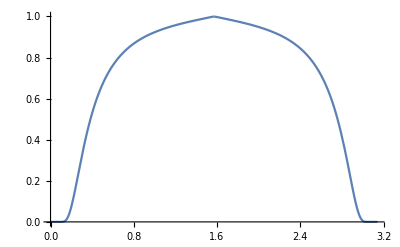

```mathematica
Plot[Pjump[1,10^13,x],{x,0,π},PlotRange->All]
```

## Generating the grid

```mathematica
Es=1;
B=10^13;
τv=τreson[Es,B];
τx1=logspace[-3,Log[10,τv],(IntegerPart[Log[10,τv]]+3)*10];
τx2=logspace[Log[10,τv],Log[10,2]+4,IntegerPart[(Log[10,2]+4-Log[10,τv])]*30];
τ=Reverse[DeleteDuplicates[Flatten[{τx1,τx2}]]];
position=IntegerPart[(Log[10,2]+4-Log[10,τv])]*30;
θx=N[Range[0.001,89.9,(89.9-0.001)/30]]/180*π;
I1u=Table[0,Length[τ],Length[θx]];
I2u=Table[0,Length[τ],Length[θx]];
I1d=Table[0,Length[τ],Length[θx]];
I2d=Table[0,Length[τ],Length[θx]];
I1u[[1]]=Flatten[Table[1/2,1,Length[θx]]*Planck[Es,temperature[First[τ]]]];
I2u[[1]]=Flatten[Table[1/2,1,Length[θx]]*Planck[Es,temperature[First[τ]]]];
I1d[[Length[τ]]]=Flatten[Table[0,1,Length[θx]]];
I2d[[Length[τ]]]=Flatten[Table[0,1,Length[θx]]];
(*give the initial data for source function*)
S1=Table[0,Length[τ],Length[θx]];
S2=Table[0,Length[τ],Length[θx]];

u1=Table[0,Length[τ]];
u2=Table[0,Length[τ]];
δτ=Table[0,Length[τ]];
δτ1=Table[0,Length[τ]];
(*For[j=1,j≤Length[θx],j++,
For[
i=1,i≤Length[τ],i++,S1[[i,j]]=1/2*Planck[Es,temperature[τ[[i]]]];S2[[i,j]]=1/2*Planck[Es,temperature[τ[[i]]]]];
]*)
```

```mathematica
τv
τ[[position]]
```

0.00403765

0.00403765

```mathematica
S1[[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ff1=Table[0,{Length[τ]},{Length[θx]}];
ff2=Table[0,{Length[τ]},{Length[θx]}];
sc11=Table[0,{Length[τ]},{Length[θx]}];
sc12=Table[0,{Length[τ]},{Length[θx]}];
sc21=Table[0,{Length[τ]},{Length[θx]}];
sc22=Table[0,{Length[τ]},{Length[θx]}];
κt1=Table[0,Length[τ],Length[θx]];
κt2=Table[0,Length[τ],Length[θx]];
For[i=1,i≤Length[τ],i++,
{Ap1,Ap2,Am1,Am2,A01,A02}=Aint[Es,B,τ[[i]]];
For[j=1,j≤Length[θx],j++,
free=freeopacity[Es,B,τ[[i]],θx[[j]]];
ff1[[i,j]]=free[[1]];ff2[[i,j]]=free[[2]];
scatter=scatteropacity[Es,B,τ[[i]],θx[[j]]];
sc11[[i,j]]=scatter[[1]];
sc12[[i,j]]=scatter[[2]];
sc21[[i,j]]=scatter[[3]];
sc22[[i,j]]=scatter[[4]];
κt1[[i,j]]=ff1[[i,j]]+sc11[[i,j]]+sc21[[i,j]];
κt2[[i,j]]=ff2[[i,j]]+sc12[[i,j]]+sc22[[i,j]];
]
]
```

0.84889560.4024217320.650952390.4902723020.0001520130.607305966

0.8440581340.3906147190.6557858870.47328115130.0001559820.6361041298

0.8391896160.37763043960.6606501740.45504911870.0001602140.6673204417

0.834325760.36344209070.6655095360.43558930290.0001648530.7009686064

0.8294969330.3480302340.6703335980.41491775130.0001694730.7370520148

0.8247285010.3313847770.6750969880.39305569820.0001745110.7755595249

0.8200410820.31350729090.6797790710.37003196720.0001798280.8164607606

0.8154510.2944134890.6843635020.34588588820.0001854970.8597006228

0.8109706250.27413625430.6888378840.32067057130.0001914920.905193174

0.8066087380.25272921420.6931933940.29445685510.0001978680.9528139306

0.8023708770.23027114240.6974244430.26733809680.0002046631.00239076

0.7982596270.20687149920.7015283750.23943613920.0002119831.053692361

0.7942748470.18267758990.7055052340.21090894440.000219911.106413466

0.7904138130.1578840760.709357610.18196065770.000228581.160155266

0.7866712060.13274601850.7130906260.15285533880.000238171.214398643

0.7830388920.10759745270.7167121290.12393647370.000248981.268466074

0.7795052810.082879111370.7202332530.09565613150.000261441.32146477

0.7760538650.059182451090.7236697280.068621504850.0002763631.372196044

0.7726597780.03732594920.7270449230.04367640340.0002952921.418997647

0.7692803930.018506329610.7303979650.022065835860.0003216411.459427835

0.765818770.0046797954830.7338135530.0058668020110.0003678361.489453403

0.7618677990.00071921259040.7377002620.00048168250640.0004319361.498799102

0.758586360.011116547170.7410642730.008506729340.0003493671.480376723

0.7558295150.026078848140.7438517550.020539908980.000318731.453381243

0.7533925520.042269840320.7463074070.033724440860.0003000431.424005719

0.7511985340.058403906770.7485146570.046925003380.0002868091.39467109

0.7492032270.073915041940.7505200650.05963546340.0002767021.366449495

0.7473766180.088559701290.7523547450.071635220060.0002686481.339805062

0.7456964430.10225209250.754041580.082844204920.000261951.314903732

0.7441452240.1149861740.7555992620.093253662270.000256361.291760186

0.742708790.12679596280.7570396320.10289078190.000251581.270313255

0.7413753390.13773447970.7583772550.11179990020.00024741.25046562

0.7401348580.14786234110.7596214040.12003230510.000243741.232105354

0.7389787580.15724155920.7607807480.12764069370.000240491.215117747

0.7378996070.16593223360.7618627950.13467621490.00023761.199391551

0.7368908240.17399087920.7628741030.1411869740.0002351.184822147

0.7359468270.18146968670.7638204220.14721736870.000232651.171312945

0.7350625910.18841631290.764706270.15280789910.000230531.158775788

0.7342335870.19487396720.7655377830.15799523840.00022861.147130794

0.7334558530.20088165630.76631730.16281244550.000226831.136305898

0.7327258580.20647450690.7670489250.16728924530.000225211.126236248

0.7320404370.21168411790.7677358380.17145233410.0002237281.116863548

0.7313967520.21653891520.7683808920.17532568740.0002223631.108135397

0.7307922440.22106449320.7689866610.1789308550.0002211061.100004652

0.7302245980.22528393450.7695554620.18228723720.0002199461.092428828

0.729691710.22921810510.7700894210.18541233770.0002188751.085369557

0.729191660.23288592170.7705904610.18832199320.0002178851.078792084

0.7287226850.23630459320.7710603510.19103058020.000216971.072664826

0.7282831580.2394898360.7715007190.19355119840.0002161231.066958965

0.7278715680.24245606560.7719130920.19589583390.000215341.0616481

0.7274865040.24521656510.7722988810.19807550210.0002146161.056707932

0.7271266370.24778363310.7726594180.2001003740.0002139461.052115992

0.7267907120.25016871190.7729959620.20197988420.0002133271.047851403

0.7264775360.25238249860.773309710.20372282590.0002127551.043894675

0.7261859640.25443503960.773601810.2053374310.0002122271.040227529

0.7259148980.25633581090.7738733620.20683143860.000211741.03683275

0.725663280.25809378490.7741254290.20821215240.0002112921.033694062

0.7254300830.25971748610.7743590380.20948648840.000210881.030796025

0.7252143120.26121503520.7745751870.2106610140.0002105021.02812395

0.7250150.26259418550.7747748460.21174197920.0002101541.025663835

0.7248312080.26386235020.7749589560.21273534190.0002098371.023402307

0.7246620210.26502662330.7751284330.21364678670.0002095461.021326589

0.7245065530.26609379560.7752841660.21448174030.0002092821.019424464

0.7243639420.26707036460.7754270170.21524538170.0002090411.017684253

0.7242333560.2679625420.7755578220.21594265030.0002088221.016094807

0.724113990.26877625830.7756773870.21657825120.0002086241.01464549

0.7240050680.26951716460.7757864860.21715665910.0002084461.013326176

0.7239058490.27019063370.7758858660.21768212050.0002082851.012127245

0.7238156220.27080176110.7759762380.21815865610.000208141.011039582

0.7237337090.27135536450.776058280.21859006190.0002080111.010054573

0.7236594680.27185598430.7761326360.21897991160.0002078971.009164104

0.7235922940.27230788470.7761999110.21933155770.0002077951.008360557

0.7235316170.27271505520.7762606780.21964813460.0002077061.00763681

0.7234769050.27308121270.7763154680.21993256140.0002076271.006986225

0.7234276620.27340980460.7763647790.22018754520.0002075591.00640265

0.7233834330.27370401270.7764090670.22041558530.0002075011.005880401

0.7233437960.27396675780.7764487530.22061897790.0002074511.005414264

0.7233082970.27420119560.7764842940.22080019970.0002074091.004998604

0.7232755690.27441644530.7765170590.22096632350.0002073731.004617231

0.723245070.27461609240.7765475880.22112012430.0002073421.004263783

0.7232166310.27480127850.7765760540.22126248470.0002073161.003936236

0.7231900890.27497306530.7766026160.22139422350.0002072951.003632711

0.7231652960.27513244050.7766274250.22151610080.0002072791.003351458

0.7231421090.27528032270.7766506230.22162882110.0002072681.003090856

0.7231203970.27541756630.7766723420.22173303780.0002072611.002849396

0.7231000360.27554496560.7766927050.22182935590.0002072591.002625678

0.7230809080.27566325960.7767118310.22191833610.0002072621.002418404

0.7230629040.27577313540.7767298270.22200049690.0002072691.002226367

0.7230459210.27587523210.7767467990.22207631810.0002072811.002048449

0.723029860.27597014420.7767628420.22214624310.0002072981.001883612

0.723014630.27605842510.7767780510.22221068130.0002073191.001730893

0.7230001430.27614058970.7767925120.22227001060.0002073451.001589399

0.7229863160.27621711730.7768063080.22232457930.0002073771.001458303

0.7229730680.27628845480.7768195190.22237470820.0002074131.001336837

0.7229603250.27635501840.7768322210.22242069220.0002074551.001224289

0.7229480130.27641719660.7768444850.22246280230.0002075021.001120001

0.7229360610.27647535170.7768563830.22250128690.0002075561.001023361

0.7229244030.27652982280.7768679820.22253637310.0002076151.000933804

0.7229129710.27658092670.7768793480.22256826850.0002076811.000850804

0.7229017010.27662896040.7768905450.22259716190.0002077541.000773877

0.7228905290.27667420240.7769016370.22262322480.0002078341.000702572

0.7228793940.27671691480.7769126850.22264661210.0002079221.000636473

0.7228682320.2767573440.7769237510.22266746320.0002080181.000575192

0.7228569820.2767957230.7769348960.22268590280.0002081221.000518374

0.7228455810.27683227210.7769461830.22270204180.0002082361.000465686

0.7228339670.27686720040.7769576740.22271597760.000208361.000416822

0.7228220770.2769007070.776969430.22272779510.0002084941.000371498

0.7228098440.27693298230.7769815170.2227375670.0002086391.00032945

0.7227972040.27696420880.7769940.22274535420.0002087961.000290437

0.7227840880.27699456230.7770069470.22275120660.0002089661.000254231

0.7227704250.2770242130.7770204270.22275516280.0002091491.000220624

0.7227561410.27705332640.7770345120.2227572510.0002093481.000189422

0.722741160.27708206420.7770492780.22275748870.0002095621.000160447

0.7227254030.27711058530.7770648050.22275588310.0002097931.000133531

0.7227087850.27713904680.7770811730.22275243110.0002100421.000108522

0.7226912180.27716760490.7770984720.22274711910.000210311.000085276

0.7226726080.27719641540.7771167930.22273992360.00021061.000063661

0.7226528560.27722563540.7771362320.22273081010.0002109121.000043554

0.7226318570.27725542370.7771568950.22271973380.0002112491.000024842

0.7226094990.27728594160.777178890.22270663880.0002116121.000007419

0.7225856630.27731735450.7772023350.22269145790.0002120020.9999911872

0.7225602220.27734983240.7772273550.22267411220.0002124230.999976055

0.7225330390.2773835510.7772540840.22265451060.0002128780.9999619373

0.7225039680.2774186930.7772826670.22263254930.0002133670.9999487567

0.7224728510.27745544930.7773132560.22260811070.0002138940.999936439

0.722439520.277494020.7773460190.22258106310.0002144610.9999249159

0.7224037940.2775346160.7773811340.22255125940.0002150740.9999141236

0.7223654750.27757746030.7774187920.22251853620.0002157340.9999040024

0.7223243520.27762278970.7774592030.22248271280.0002164460.9998944965

0.7222801950.27767085630.7775025920.22244358910.0002172140.9998855535

0.7222327580.27772192970.7775492010.2224009450.0002180430.9998771243

0.7221817690.27777629870.7775992950.2223545380.0002189370.9998691623

0.7221269380.2778342740.777653160.22230410120.0002199030.9998616238

0.7220679450.27789619050.7777111090.22224934140.0002209470.9998544671

0.7220044450.27796241010.777773480.22218993630.0002220750.9998476527

0.7219360610.27803332510.7778406450.22212553140.0002232950.9998411426

0.7218623790.27810936170.7779130070.22205573710.0002246150.9998349003

0.7217829480.27819098390.7779910090.22198012450.0002260440.9998288906

0.7216972720.27827869860.7780751360.22189822130.0002275930.9998230792

0.7216048090.27837306010.778165920.22180950690.0002292720.9998174321

0.7215049590.27847467670.7782639480.22171340620.0002310940.9998119162

0.7213970640.27858421730.7783698640.22160928380.0002330730.999806498

0.7212803940.27870241940.7784843820.22149643580.0002352250.999801144

0.7211541410.27883009810.7786082920.22137408130.0002375670.9997958197

0.7210174110.2789681570.778742470.22124135220.000240120.99979049

0.7208692060.27911760010.778887890.2210972810.0002429050.9997851181

0.7207084120.2792795470.7790456410.22094078710.0002459480.9997796651

0.7205337840.27945524930.7792169390.22077066020.0002492780.9997740898

0.7203439230.27964611130.7794031490.22058554080.0002529290.9997683473

0.7201372530.27985371360.779605810.22038389680.0002569380.999762389

0.7199119940.28007984230.7798266570.22016399620.000261350.9997561609

0.7196661230.28032652320.7800676630.21992387350.0002662150.9997496028

0.7193973380.28059606370.780331070.21966128910.0002715930.9997426466

0.7191030020.28089110380.7806194440.2193736810.0002775550.9997352142

0.7187800840.28121467850.7809357360.21905810370.0002814360.9997299615

0.7184250790.2815702950.7812833520.21871115460.0002887610.999721358

0.7180339160.28196202920.7816662460.21832888110.0002998380.9997090891

0.7176018320.28239464610.7820890410.21790666490.0003091270.9996986885

0.7171232210.2828737540.7825571710.21743907440.0003196080.9996871712

0.7165914370.28340600090.7830770720.2169196770.0003314910.9996743219

0.7159985410.28399932950.7836564230.21634079460.0003450360.9996598758

0.7153349620.28466331250.784304470.21569318490.0003605570.9996435138

0.7145890530.2854095980.7850324450.21496561730.0003784590.9996248279

0.7137464910.2862525110.785854140.21414430170.0003993040.9996032519

0.7127894510.28720987990.7867866890.21321210680.000423860.9995780135

0.7116954460.28830419150.7878516560.21214746920.0004528980.9995483396

0.7104356830.28956424180.789076590.21092284180.0004877270.9995129166

```mathematica
For[k=1,k≤15,k++,
For[j=1,j≤Length[θx],j++,
θ=θx[[j]];μ=Cos[θ];
For[m=1,m≤Length[τ],m++,
u1[[m]]=2*π/c*(Integrate[Interpolation[Transpose@{θx,Sin[θx]*(I1u[[m]]+I1d[[m]])},InterpolationOrder->3][t],{t,Min[θx],Max[θx]}]);
u2[[m]]=2*π/c*Integrate[Interpolation[Transpose@{θx,Sin[θx]*(I2u[[m]]+I2d[[m]])},InterpolationOrder->3][t],{t,Min[θx],Max[θx]}];
S1[[m]]=ff1[[m]]/κt1[[m]]*Planck[Es,temperature[τ[[m]]]]/2+sc11[[m]]/κt1[[m]]*(c u1[[m]])/(4 π)+sc21[[m]]/κt1[[m]]*(c u2[[m]])/(4 π);
S2[[m]]=ff2[[m]]/κt2[[m]]*Planck[Es,temperature[τ[[m]]]]/2+sc12[[m]]/κt2[[m]]*(c u1[[m]])/(4 π)+sc22[[m]]/κt2[[m]]*(c u2[[m]])/(4 π);
];
(*upward integration and downward integration*)
For[i=2,i≤Length[τ],i++,
δτ[[i]]=τ[[i]]-τ[[i-1]];
I1u[[i,j]]=1/(1-(δτ[[i]]* κt1[[i,j]])/(2*μ*κT))((1+(δτ[[i]]* κt1[[i-1,j]])/(2*μ*κT))I1u[[i-1,j]]-δτ[[i]]/(2*μ*κT)*(κt1[[i-1,j]]*S1[[i-1,j]]+κt1[[i,j]]*S1[[i,j]]));
I2u[[i,j]]=1/(1-(δτ[[i]]* κt2[[i,j]])/(2*μ*κT))((1+(δτ[[i]]* κt2[[i-1,j]])/(2*μ*κT))I2u[[i-1,j]]-δτ[[i]]/(2*μ*κT)*(κt2[[i-1,j]]*S2[[i-1,j]]+κt2[[i,j]]*S2[[i,j]]));
a=I1u[[i,j]];
b=I2u[[i,j]];
If[i==position,
I1u[[i,j]]=Pjump[Es,B,θ]*a+(1-Pjump[Es,B,θ])*b;
I2u[[i,j]]=Pjump[Es,B,θ]*b+(1-Pjump[Es,B,θ])*a,
I1u[[i,j]]=a;I2u[[i,j]]=b
];

i1=Length[τ]+1-i;
δτ1[[i1]]=τ[[i1]]-τ[[i1+1]];
I1d[[i1,j]]=1/(1+(δτ1[[i1]]* κt1[[i1,j]])/(2*μ*κT))((1-(δτ1[[i1]]* κt1[[i1+1,j]])/(2*μ*κT))I1d[[i1+1,j]]+δτ1[[i1]]/(2*μ*κT)*(κt1[[i1+1,j]]*S1[[i1+1,j]]+κt1[[i1,j]]*S1[[i1,j]]));
I2d[[i1,j]]=1/(1+(δτ1[[i1]]* κt2[[i1,j]])/(2*μ*κT))((1-(δτ1[[i1]]* κt2[[i1+1,j]])/(2*μ*κT))I2d[[i1+1,j]]+δτ1[[i1]]/(2*μ*κT)*(κt2[[i1+1,j]]*S2[[i1+1,j]]+κt2[[i1,j]]*S2[[i1,j]]));
ax=I1d[[i1,j]];
bx=I2d[[i1,j]];

If[i1==Length[τ]+1-position,
I1d[[i1,j]]=Pjump[Es,B,θ]*ax+(1-Pjump[Es,B,θ])*bx;
I2d[[i1,j]]=Pjump[Es,B,θ]*bx+(1-Pjump[Es,B,θ])*ax,
I1d[[i1,j]]=ax;I2d[[i1,j]]=bx
];

];

];
]
```

General::munfl: Exp[-3.43476×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
I2u[[-1]]
```

{18513.1,15476.5,13780.,13989.4,14236.2,13788.6,12847.2,11724.4,10606.9,9576.23,8657.69,7850.65,7144.42,6525.43,5980.38,5497.31,5065.91,4677.44,4324.53,4000.92,3701.28,3420.97,3155.92,2902.48,2657.35,2417.57,2180.69,1945.62,1715.97,1519.18,2171.26}

```mathematica
I1u[[-1]]
```

{18526.4,14649.1,11072.,9189.31,8559.26,8959.23,9900.35,10993.7,12040.4,12964.7,13751.3,14409.4,14956.6,15410.9,15788.3,16102.,16362.6,16577.8,16753.3,16892.6,16996.9,17065.4,17094.4,17076.5,16998.8,16839.3,16560.2,16091.4,15288.9,13761.2,6476.5}

```mathematica
(I1u[[-1]]+I2u[[-1]])Cos[θx]
```

{37039.6,30084.4,24716.1,22894.2,22299.1,21975.5,21638.2,21214.4,20695.7,20091.7,19415.5,18678.8,17891.3,17060.1,16190.9,15287.9,14354.6,13393.7,12407.8,11399.2,10370.,9322.67,8259.64,7183.87,6098.94,5009.54,3922.29,2847.42,1802.58,822.82,13.8043}

```mathematica
data=Transpose@{θx,I1u[[-1]],I2u[[-1]]};
SetDirectory[NotebookDirectory[]]
Export["first.dat",data];
```

/Users/yonggao/Desktop/paper_calc/X-ray

```mathematica
x=2;y=3;z=7;
If[x≤4,y=x+3;z=y*2]
```

10

```mathematica
z
```

10

```mathematica
ff1[[2]]/κt1[[2]]
```

{0.999956,0.999958,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999959,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958,0.999958}

```mathematica
Planck[Es,temperature[τ[[2]]]]/2
```

99899.8

```mathematica
xx={1,2,3,4,5};
yy={5,4,3,2,1};
xx*yy
```

{5,8,9,8,5}

```mathematica
sc11[[50]]/κt1[[50]]*(c u1[[50]])/(4 π)
```

{49.4772,4.88983,2.36366,2.67991,3.83423,5.47707,7.46716,9.71574,12.1519,14.7138,17.3463,20.001,22.6359,25.2159,27.7119,30.101,32.3652,34.4909,36.4686,38.2917,39.9561,41.4597,42.8015,43.9819,45.0017,45.8622,46.5647,47.1105,47.501,47.7369,47.8189}